Node A: Normal(20, 1)

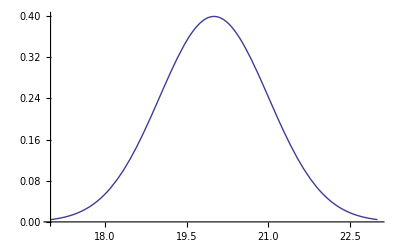

```mathematica
Plot[PDF[NormalDistribution[20,1],x],{x,17,23}]
```

Node E: Beta(1, 1)

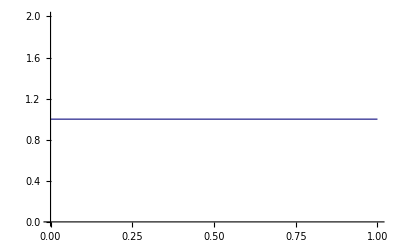

```mathematica
Plot[PDF[BetaDistribution[1,1],x],{x,0,1},PlotRange->All]
```

Node B: Gamma(A^Pi, 1/7)

```mathematica
Manipulate[Plot[PDF[GammaDistribution[a^Pi,1/7],x],{x,0,5000},PlotRange->0.1],{{a,20},16,24}]
```

Node D: Beta(A, E)

```mathematica
Manipulate[Plot[PDF[BetaDistribution[alpha,beta],x],{x,0.0001,1},PlotRange->All],{{alpha,20},16,24},{{beta,0.785},0.0001,1}]
```

Node C: Bernoulli(D)

```mathematica
Manipulate[DiscretePlot[PDF[BernoulliDistribution[p],x],{x,0,1},PlotRange->All],{p,0,1}]
```

Node F: Poisson(D)

```mathematica
Manipulate[DiscretePlot[PDF[PoissonDistribution[rate],x],{x,0,10},PlotRange->All,PlotMarkers->Automatic],{rate,0.001,1}]
```

Node G: Normal(E, F)

```mathematica
Manipulate[Plot[PDF[NormalDistribution[mean,var],x],{x,-4,5},PlotRange->{0,1}],{mean,0,1},{var,0.0001,4}]
```